```mathematica
possibleMasses=Table[If[Length[NSolve[specificDrag==2dragCoefficient airDensity dragArea (payloadMass+dragArea dragMassPerArea+.5(springMass+hingeMass))totalEnergy/((payloadMass+dragArea dragMassPerArea+springMass+hingeMass)^3 gravity)&&dragArea>0,dragArea]]>0,True,False],{payloadMass,0,5,.01},{dragMassPerArea,0,1,.01}];
```

```mathematica
Show[ArrayPlot[possibleMasses/.{True->1,False->0}],Graphics[{Red,Line[{{48,0},{48,500}}],Blue,Line[{{0,400},{100,400}}]}]]
```

-Graphics-

```mathematica
(Total[possibleMasses⟦All,49⟧/.{True->1,False->0}]-2)/100.
```

0.08

```mathematica
ClearAll[specificDrag]
specificDrag[dragArea_,payloadMass_,length_]:=2dragCoefficient airDensity dragArea (payloadMass+dragArea dragMassPerArea+.5(density numberOfSprings width thickness length+hingeMass))totalEnergy/((payloadMass+dragArea dragMassPerArea+density numberOfSprings width thickness length+hingeMass)^3 gravity)
```

```mathematica
ClearAll[efficiency]
efficiency[dragArea_,payloadMass_,length_]:=(payloadMass+.5(density numberOfSprings width thickness length+hingeMass))/(payloadMass+dragArea dragMassPerArea+density numberOfSprings width thickness length+hingeMass)
```

```mathematica
ClearAll[velocity]
velocity[dragArea_,payloadMass_,length_]:=√((2efficiency[dragArea,payloadMass]springEnergy[length,10])/(payloadMass+dragArea dragMassPerArea+density numberOfSprings width thickness length+hingeMass))
```

```mathematica
ClearAll[springEnergy]
springEnergy[length_,numberOfElements_]:=With[{compressedLength=.23length,dLength=uncompressedLength/numberOfElements,secondMomentOfArea=width thickness^3/12,energy=Function[{deflection},Total[numberOfElements elasticModulus width thickness^3 deflection^2/(24uncompressedLength) ]],deflection=Array[d,numberOfElements]},Minimize[{energy[deflection],Total[dLength Cos[Accumulate[deflection]]]==0,Total[dLength Sin[Accumulate[deflection]]]==0},deflection]]
```

```mathematica
springEnergy[uncompressedLength,numberOfElements]
```

{0.326382,{d[1]→-1.08136×10^-8,d[2]→0.165138,d[3]→0.350124,d[4]→0.560063,d[5]→0.756854,d[6]→0.844074,d[7]→0.756854,d[8]→0.560063,d[9]→0.350124,d[10]→0.165138}}

```mathematica
uncompressedLength=.25;
compressedLength=.23uncompressedLength;
width=.0047752;
thickness=.0004826;
numberOfSprings=4;
elasticModulus=131 10^9;
density=1500;
numberOfElements=10;
dragCoefficient=1.4;
airDensity=1.225;
gravity=9.81;
hingeMass=0.02;
```

```mathematica
desiredVelocity=10;
desiredVelocityMargin=10;
NSolve[{specificDrag[dragArea,payloadMass]==10,Abs[velocity[dragArea,payloadMass]-desiredVelocity]<desiredVelocityMargin},{dragArea,payloadMass}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(121001 dragArea)/175984-(92291 payloadMass)/87992 == 1.

{}

```mathematica
contours={0.01,0.1,1.,10.,100.};
contourColors=ColorData["PigeonTones"]/@Subdivide[Length@contours];
```

```mathematica
velocities=Import[NotebookDirectory[]<>"velocity.csv", "CSV"];
specificDrags=Import[NotebookDirectory[]<>"specificDrag.csv", "CSV"];
dataRange={{0.005,.205},{.10,1}};
```

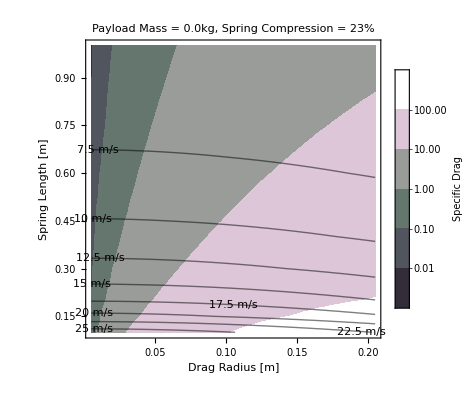

```mathematica
Show[ListContourPlot[specificDrags,PlotRange->All,Contours->contours,ContourStyle->None,DataRange->dataRange,ContourShading->contourColors,PlotLegends->BarLegend[Automatic,LegendLabel->"Specific Drag"],FrameLabel->{"Drag Radius [m]","Spring Length [m]"},PlotLabel->"Payload Mass = 0.0kg, Spring Compression = 23%"],ListContourPlot[velocities,ContourShading->None,ContourStyle->Thick,ContourLabels->Function[{x,y,z},Text[Quantity[z,"meters per second"],{x,y},Background->White]],DataRange->dataRange],ImageSize->Full]
```

```mathematica
Export[NotebookDirectory[]<>DateString[{"Year",".","Month",".","Day",".","Hour24",".","Minute"}]<>"_JumperConfigurationSpace.png",%]
```

/Users/fp/projects/Jumping Robots/2019.7.26.14.34_JumperConfigurationSpace.png

```mathematica
specificDrags//MatrixForm
```

(0.27831 | 2.4961 | 6.886 | 13.358 | 21.783 | 31.993 | 43.794 | 56.967 | 71.277 | 86.481 | 102.33 | 118.6 | 135.04 | 151.45 | 167.63 | 183.4 | 198.62 | 213.16 | 226.9 | 239.78 | 251.72
0.16412 | 1.4722 | 4.063 | 7.8861 | 12.869 | 18.918 | 25.923 | 33.761 | 42.298 | 51.396 | 60.914 | 70.713 | 80.66 | 90.629 | 100.5 | 110.18 | 119.56 | 128.57 | 137.15 | 145.23 | 152.78
0.10963 | 0.98363 | 2.7154 | 5.2732 | 8.6106 | 12.668 | 17.376 | 22.653 | 28.416 | 34.574 | 41.035 | 47.71 | 54.509 | 61.349 | 68.152 | 74.847 | 81.37 | 87.667 | 93.691 | 99.403 | 104.77
0.078601 | 0.70532 | 1.9477 | 3.784 | 6.1826 | 9.1026 | 12.496 | 16.307 | 20.478 | 24.946 | 29.646 | 34.516 | 39.493 | 44.517 | 49.533 | 54.488 | 59.338 | 64.04 | 68.56 | 72.868 | 76.941
0.059029 | 0.52976 | 1.4633 | 2.8441 | 4.6493 | 6.8497 | 9.4103 | 12.292 | 15.451 | 18.842 | 22.42 | 26.136 | 29.944 | 33.801 | 37.665 | 41.496 | 45.26 | 48.925 | 52.462 | 55.85 | 59.068
0.045827 | 0.41133 | 1.1365 | 2.2096 | 3.6139 | 5.3274 | 7.3242 | 9.5747 | 12.047 | 14.706 | 17.517 | 20.444 | 23.452 | 26.507 | 29.577 | 32.631 | 35.642 | 38.585 | 41.437 | 44.18 | 46.798
0.036485 | 0.32752 | 0.9051 | 1.7604 | 2.8804 | 4.2486 | 5.8448 | 7.6464 | 9.6286 | 11.765 | 14.028 | 16.389 | 18.822 | 21.3 | 23.797 | 26.288 | 28.752 | 31.169 | 33.519 | 35.789 | 37.963
0.029632 | 0.26603 | 0.73532 | 1.4306 | 2.3418 | 3.4559 | 4.7572 | 6.2278 | 7.8483 | 9.5977 | 11.454 | 13.396 | 15.401 | 17.448 | 19.516 | 21.585 | 23.638 | 25.657 | 27.628 | 29.537 | 31.374
0.02446 | 0.21962 | 0.60716 | 1.1816 | 1.935 | 2.8568 | 3.9347 | 5.1544 | 6.5002 | 7.9554 | 9.5025 | 11.124 | 12.801 | 14.517 | 16.255 | 17.999 | 19.734 | 21.445 | 23.12 | 24.749 | 26.32
0.020467 | 0.18378 | 0.50818 | 0.98925 | 1.6205 | 2.3936 | 3.2984 | 4.3234 | 5.4559 | 6.6822 | 7.988 | 9.3589 | 10.78 | 12.237 | 13.716 | 15.203 | 16.686 | 18.153 | 19.594 | 20.998 | 22.358
0.017325 | 0.15558 | 0.43027 | 0.83778 | 1.3728 | 2.0286 | 2.7967 | 3.6679 | 4.6315 | 5.6764 | 6.7907 | 7.9624 | 9.1794 | 10.429 | 11.701 | 12.982 | 14.263 | 15.533 | 16.784 | 18.006 | 19.194
0.014812 | 0.13302 | 0.36794 | 0.71659 | 1.1746 | 1.7363 | 2.3949 | 3.1424 | 3.9703 | 4.8691 | 5.829 | 6.8399 | 7.8916 | 8.9738 | 10.077 | 11.19 | 12.306 | 13.415 | 14.51 | 15.583 | 16.628
0.012774 | 0.11473 | 0.3174 | 0.61829 | 1.0138 | 1.4991 | 2.0685 | 2.7155 | 3.4327 | 4.2123 | 5.046 | 5.9253 | 6.8414 | 7.7858 | 8.7498 | 9.7254 | 10.705 | 11.68 | 12.645 | 13.593 | 14.519
0.011103 | 0.099724 | 0.27591 | 0.53758 | 0.88166 | 1.3042 | 1.8003 | 2.3644 | 2.9904 | 3.6716 | 4.401 | 5.1712 | 5.975 | 6.8048 | 7.6533 | 8.5136 | 9.3787 | 10.242 | 11.098 | 11.941 | 12.766
0.009716 | 0.087275 | 0.2415 | 0.47062 | 0.77204 | 1.1424 | 1.5775 | 2.0727 | 2.6227 | 3.2218 | 3.8641 | 4.5431 | 5.2527 | 5.9864 | 6.7378 | 7.5009 | 8.2697 | 9.0386 | 9.8023 | 10.556 | 11.295
0.0085553 | 0.076854 | 0.21269 | 0.41455 | 0.6802 | 1.0068 | 1.3907 | 1.828 | 2.3141 | 2.8442 | 3.413 | 4.0151 | 4.6451 | 5.2974 | 5.9665 | 6.647 | 7.3338 | 8.0219 | 8.7067 | 9.3839 | 10.049
0.0075755 | 0.068056 | 0.18836 | 0.36719 | 0.60263 | 0.89219 | 1.2328 | 1.6211 | 2.0531 | 2.5245 | 3.0309 | 3.5676 | 4.1298 | 4.7126 | 5.3113 | 5.9212 | 6.5376 | 7.1563 | 7.7731 | 8.3842 | 8.9859
0.006742 | 0.060571 | 0.16766 | 0.3269 | 0.53661 | 0.79465 | 1.0984 | 1.4448 | 1.8305 | 2.2519 | 2.7049 | 3.1855 | 3.6895 | 4.2127 | 4.7508 | 5.2997 | 5.8554 | 6.414 | 6.9719 | 7.5255 | 8.0717
0.0060282 | 0.054161 | 0.14993 | 0.29237 | 0.48003 | 0.71104 | 0.98311 | 1.2936 | 1.6396 | 2.0178 | 2.4248 | 2.857 | 3.3108 | 3.7824 | 4.2681 | 4.7642 | 5.2671 | 5.7734 | 6.2798 | 6.7832 | 7.2808)